#### 1)

```mathematica
f=3/x^4-3/((x^3)^(1/4));
g=Sin[x]/ArcSin[x];
h=Exp[2x]Cos[3x+2];
D[f,x]
D[g,x]
D[h,x]
```

-12/x^5+(9 x^2)/(4 (x^3)^(5/4))

Cos[x]/ArcSin[x]-Sin[x]/(√(1-x^2) ArcSin[x]^2)

2 ⅇ^(2 x) Cos[2+3 x]-3 ⅇ^(2 x) Sin[2+3 x]

#### 2)

```mathematica
f=Log[x];
Series[f,{x,1,2}]//Normal
%/.{x->1.1}
Log[1.1]
```

-1-1/2 (-1+x)^2+x

0.095

0.0953102

#### 3)

-24 x-4 x^2+4 x^3+x^4

-24-8 x+12 x^2+4 x^3

{{x→-3},{x→-√2},{x→√2}}

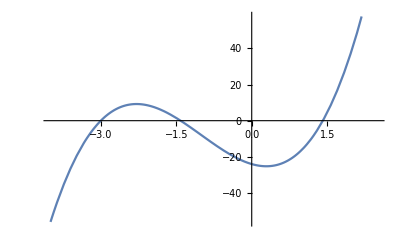

```mathematica
(x+3)(x^2-2)//Expand;
y1=Integrate[%,x]4//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-4,2.5}]
```

#### 4)

```mathematica
-3/(x+2)+4/(x-3)//Together;
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
```

(17+x)/(-6-x+x^2)

4 Log[3-x]-3 Log[2+x]

#### 5)

```mathematica
Integrate[x^2-1/x^2,{x,1,2}]
Integrate[Cos[x]/(Sin[x]^2+1),{x,0,π/2}]
```

11/6

π/4

#### 6)

-3+2 x+x^2

{{x→-3},{x→1}}

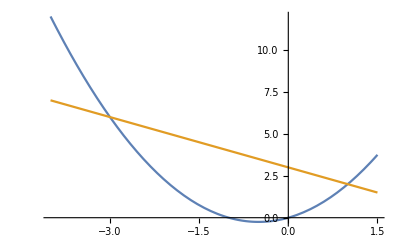

32/3

```mathematica
(x-1)(x+3)//Expand
y1=x^2+x;
y2=3-x;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-4,1.5}]
Integrate[y2-y1,{x,-3,1}]
```

#### 7)

-5+6 x

1

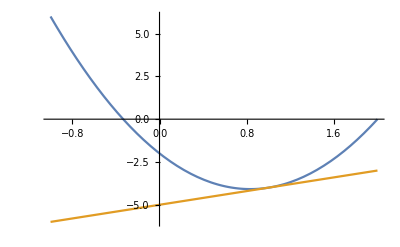

-5+x

```mathematica
f1[x_]:=3 x^2-5x-2;
f1'[x]
x0=1;
f1'[x0]
g1[x_]:=f1'[x0](x-x0)+f1[x0];
Plot[{f1[x],g1[x]},{x,-1,2}]
g1[x]
```

#### 8)

```mathematica
y1=x;
y2=2x;
S=Integrate[(y2-y1),{x,0,2}]
Sy=Integrate[(y2-y1)x,{x,0,2}]
Sx=1/2Integrate[y2^2-y1^2,{x,0,2}]
```

2

8/3

4